```mathematica
Ea[n_,k_]:= Ea[n-1,k]-1/2 (Ha[n-1,k]-Ha[n-1,k-1])
```

```mathematica
Ha[n_,k_]:= Ha[n-1,k]-1/2 (Ea[n-1,k+1]-Ea[n-1,k])
```

```mathematica
Ea[n_,0]=0
```

0

```mathematica
Ea[n_,50]=0
```

0

```mathematica
Ha[0,k_]= 0
```

0

```mathematica
Ea[0,k_]=If[Abs[k-6]< 5,1,0]
```

If[Abs[-6+k]<5,1,0]

```mathematica
Ea[1,1]
```

0

```mathematica
magfield =Table[Ea[10,k],{k,0,50}]
```

{0,-1755/512,2227/1024,687/1024,-139/128,853/1024,511/512,853/1024,-139/128,43/64,1199/512,-687/512,21/64,267/128,171/1024,1/1024,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

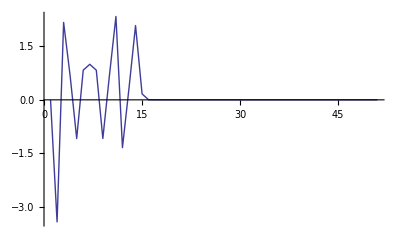

```mathematica
ListPlot[magfield,PlotJoined -> True,PlotRange -> All]
```

```mathematica
Ha
```